Your Title Here

```mathematica
Manipulate[
Module[{ρ,SG1,SG2,SG3,γ1,γ2,γ3,L,r0,r1,x1,y1,δ1,δ2,h1,L2,col1,col2,col3,UTube,incline},
ρ=1000;(*water kg/m3*)
SG1=1;(*water*)SG2=13.6;(*Hg*)SG3=0.9;(*oil*)
γ1=SG1*ρ;γ2=SG2*ρ;γ3=SG3*ρ;

L=1;r0=0.12;r1=0.05;x1=0.25/2;y1=0.25;δ1=r1/2;δ2=δ1+x1/4;

h1=y1-2*r1;L2=0.7;

col1=GrayLevel@0.6;col2=Blue;col3=GrayLevel@0.8;

incline=Graphics3D[{
(*fluid 1*)
{col1,Sphere[{-r0-x1,0,y1},r0],Tube[{{-x1,0,y1},{0,0,y1},{0,0,y1-h1}},r1]},
(*fluid 2*)
{col2,Tube[{{0,0,y1-h1},{0,0,0},{L2*Cos[θ],0,L2*Sin[θ]}},r1]},
(*fluid 3*)
{col3,Sphere[{r0+L*Cos[θ]+x1,0,L*Sin[θ]},r0],Tube[{{L2*Cos[θ],0,L2*Sin[θ]},{L*Cos[θ],0,L*Sin[θ]},{L*Cos[θ]+x1,0,L*Sin[θ]}},r1]},
},PlotRange->{{-2*r0-x1,2*r0+L*Cos[10°]+x1},{-r0,r0},{-r1,L*Sin[45°]+r0}}];

Show[incline,Boxed->False,ViewPoint->Front,ImageSize->{500,400},Axes->True]
],
Grid[{
{Control[{{θ,30 °,"angle"},10°,45 °,1 °,Appearance->"Labeled"}],SpanFromLeft},
{Style["fluid pressure (bar)",Bold],
Control[{{pA,1,Subscript[Style["P",Italic],"A"]},0.2,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{pB,1,Subscript[Style["P",Italic],"B"]},0.2,5,0.1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left]
]
```

```mathematica
incline=Graphics3D[{
{col1,Sphere[{-r0-x1,0,y1},r0]},
{col3,Sphere[{r0+L*Cos[θ]+x1,0,L*Sin[θ]},r0]},
Tube[{{-x1,0,y1},{0,0,y1},{0,0,0},{L*Cos[θ],0,L*Sin[θ]},{L*Cos[θ]+x1,0,L*Sin[θ]}},r1],
{col2,Tube[{{0,0,y1-h1},{0,0,0},{L2*Cos[θ],0,L2*Sin[θ]}},1.01*r1]},
},PlotRange->{{-2*r0-x1,2*r0+L*Cos[10°]+x1},{-r0,r0},{-r1,L*Sin[45°]+r0}}];
```

```mathematica
(*col2,Line[{{L2*Cos[θ],0,L2*Sin[θ]+r1},{L2*Cos[θ]+2*r1,0,L2*Sin[θ]+r1}}]*)
(*{col2,
Tube[{{0,0,y1-h1},{0,0,0}},1.01*r1],
GeometricTransformation[
Cylinder[{{0,0,0},{L2*Cos[θ],0,L2*Sin[θ]}},1.01*r1],
ShearingTransform[-θ,{L2*Cos[θ],0,L2*Sin[θ]},{-L2*Cos[θ],0,L2*Sin[θ]}]]}*)
```

```mathematica
L=1;r0=0.12;r1=0.05;x1=0.25;y1=0.5;δ1=r1/2;δ2=δ1+x1/4;

col1=GrayLevel@0.6;col2=Blue;col3=GrayLevel@0.8;

incline=Graphics3D[{
{col1,Sphere[{-r0-x1/2,0,y1/2},r0]},
{col3,Sphere[{r0+L*Cos[θ]+x1/2,0,L*Sin[θ]},r0]},
Tube[{{-x1/2,0,y1/2},{0,0,y1/2},{0,0,0},{L*Cos[θ],0,L*Sin[θ]},{L*Cos[θ]+x1/2,0,L*Sin[θ]}},r1]
},PlotRange->{{-2*r0-x1/2,2*r0+L*Cos[10°]+x1/2},{-r0,r0},{-r1,L*Sin[45°]+r0}}];
```

```mathematica
UTube=Graphics3D[{
{col1,Sphere[{-r0,0,y1/2},r0]},
{col3,Sphere[{2.5*x1+r0,0,y1},r0]},
Tube[{{0,0,y1/2},{x1/2,0,y1/2},{x1/2,0,0},{2*x1,0,0},{2*x1,0,y1},{2.5*x1,0,y1}},r1]
}];
```

```mathematica
Module[{},
δ1=0.1;L2=8;θ=30°;
h1=3;h2=L2*Sin[θ];h3=

Graphics3D[{
Tube[{{0,0,h1+δ1}
},Boxed->False,ViewPoint->Front,ImageSize->500]
]
```

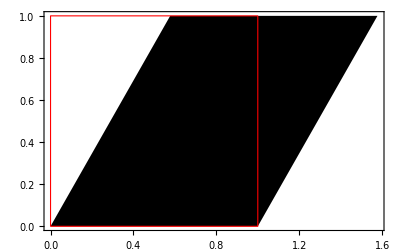





```mathematica
Graphics[{
GeometricTransformation[Rectangle[{0,0},{1,1}],ShearingTransform[30°,{1,0},{0,1}]],
EdgeForm@{Thick,Red},FaceForm@None,Rectangle[{0,0},{1,1}]
}, Frame->True]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX